# 酒精在体内代谢的数学模型建立和应用

假设胃里的酒精被吸收进入血液的速度与胃中的酒量x成正比，比例常数为k1，血液中的酒被排除的速度与血液的酒量y成正比，比例系数为k2，G为短时间内喝入胃的酒精总量,H为血液中的酒精总量,则有以下方程：
D[x]=-k1*x
D[y]=k1*x-k2*y
x[0]=G
y[0]=H
可以解得：
y=G*k1/(k2-k1)*(e^(-k1*x))+C*(e^(-k1*x))，其中C由H确定。

```mathematica
(*导入数据*)
data2004={0.25,0.5,0.75,1,1.5,2,2.5,3,3.5,4,4.5,5,6,7,8,9,10,11,12,13,14,15,16,30,68,75,82,82,77,68,68,58,51,50,41,38,35,28,25,18,15,12,10,7,7,4};
len=Length[data2004]/2;
data=Table[data2004[[{i,i+len}]],{i,1,23}];
point=ListPlot[data,PlotStyle->Hue[0,0.8,1]];
```

```mathematica
(*确定相关参数k1,k2*)
model=g*(Exp[-k2*x]-Exp[-k1*x]);
approx=FindFit[data,model,{g,k1,k2},x];
params=model/.approx
approxfunc=Plot[params,{x,0,16},PlotStyle->Green];
c1=k1/.approx
c2=k2/.approx

g/.approx;
G0=(c1-c2)*(g/.approx)/(2*c1)(*初始胃中酒量*)
```

114.433 (-ⅇ^(-2.00794 x)+ⅇ^(-0.185502 x))

2.00794

0.185502

51.9304

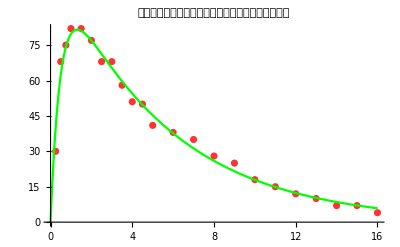

0.992896

```mathematica
(*绘图展示结果(两瓶啤酒)*)
Show[{point,approxfunc},PlotRange->All,PlotLabel->"血液中酒精含量（毫克／百毫升）随时间变化的图像"]
(*计算相关系数*)
fact=Transpose[data][[2]];
prediction=Table[params/.{x->data[[i,1]]},{i,1,len}];
Correlation[fact,prediction]
```

```mathematica
blood[g_,h_,x_]:=g*c1/(c2-c1)*Exp[-c1*x]+(h-g*c1/(c2-c1))*Exp[-c2*x];(*构建血液含酒量模型*)
stomach[g_,x_]:=g*Exp[-c1*x](*构建肠胃含酒量模型*)
```

## 大李的情况分析

在大李中午12点喝酒时，可以认为其胃中酒量是从0开始变化，且血液中无酒精存在。

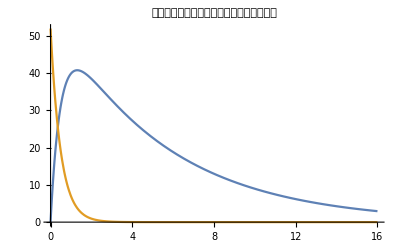

```mathematica
Plot[{blood[G0,0,x],stomach[G0,x]},{x,0,16},PlotLabel->"大李中午喝完酒后血液酒精含量变化示意图"]
```

在大李下午6点喝酒前，可以认为其胃中没有酒存在，但是其血液中仍然存在未完全代谢的酒精。

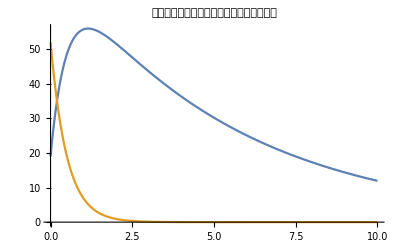

```mathematica
Plot[{blood[G0,19,x],stomach[G0,x]},{x,0,10},PlotLabel->"大李下午喝完酒后血液酒精含量变化示意图"]
```

```mathematica
MatrixForm[Table[{x,blood[G0,19,x]},{x,1,8}]]
```

(1 | 55.6297
2 | 51.5609
3 | 43.5493
4 | 36.2723
5 | 30.1439
6 | 25.0419
7 | 20.8022
8 | 17.2802)

因此，大李碰到这个问题的原因是体内酒精没有完全代谢。

## 喝了 3 瓶啤酒后多长时间内驾车就会违反上述标准

### 酒是在很短时间内喝的

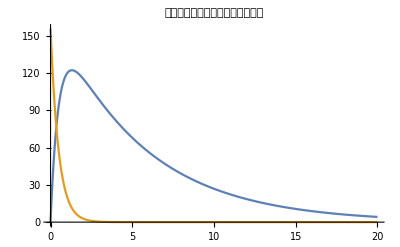

```mathematica
Plot[{blood[3*G0,0,x],stomach[3*G0,x]},{x,0,20},PlotLabel->"喝完酒后血液酒精含量变化示意图"]
```

```mathematica
FindRoot[blood[3*G0,0,x]==20,{x,12}]
```

{x→11.5887}

在短时间喝酒的情况下，大约需要11 .58 小时可以开车。

### 酒是在较长一段时间（比如 2 小时）内喝的

不妨假设酒精以匀速进入肠胃。
则在x<2时，肠胃中酒精的方程可以修改为：
D[x]=k3*x-k1*x

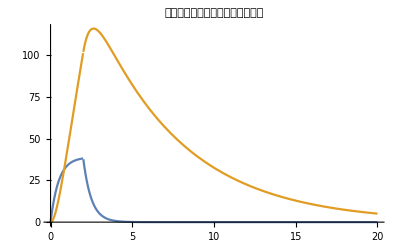

```mathematica
k3=3*G0/2;
result=DSolve[{x'[t]==k3-c1*x[t],y'[t]==c1*x[t]-c2*y[t],x[0]==0,y[0]==0},{x[t],y[t]},t];
resultx=x[t]/.result;
resulty=y[t]/.result;

funcx[x_]:=resultx/.{t->x};
funcy[x_]:=resulty/.{t->x};
stom=resultx/.{t->2};
blo=resulty/.{t->2};

listx={{funcx[x],x>0 && x≤2},{stomach[stom,x-2],x>2}};
listy={{funcy[x],x>0 && x≤2},{blood[stom,blo,x-2],x>2}};

(*生成肠胃和血液内酒精含量关于时间x的函数关系式*)
picturex=Piecewise[listx];
picturey=Piecewise[listy];
Plot[{picturex,picturey},{x,0,20},PlotLabel->"喝完酒后血液酒精含量变化示意图"]
```

```mathematica
FindRoot[picturey==20,{x,12}]
```

{x→12.6195}

在持续喝酒的情况下，大约需要12 .6 小时可以开车。

### 对比

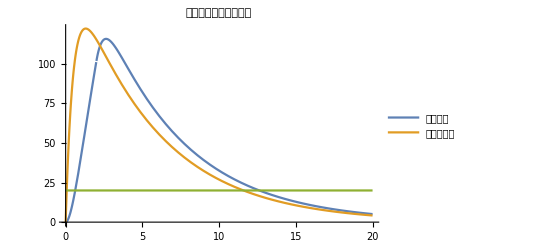

```mathematica
Plot[{picturey,blood[3*G0,0,x],20},{x,0,20},PlotLegends->{"持续喝酒","一次性喝酒"},PlotLabel->"两种情况的对比示意图"]
```

## 样估计血液中的酒精含量何时达到最高

```mathematica
Maximize[blood[3*G0,0,x],x]
```

{122.251,{x→1.30693}}

```mathematica
Maximize[blood[stom,blo,x-2],x]
```

{115.743,{x→2.63274}}

当酒是在很短时间内喝的时，其最高峰一般在1~1.5 h内达到
酒是在较长一段时间 （比如 2 小时） 内喝的时，其最高峰一般饮酒结束后0 .5 h附近达到

## 如果天天喝酒，是否还能开车？

```mathematica
res=x/.FindRoot[blood[x,0,24]==2,{x,100}]
n=res/G0
```

155.751

2.99923

根据结果可知，在每天饮酒量小于3瓶啤酒或等量酒精时，对第二天的影响很小。但是，在饮酒量超过3瓶啤酒时，对第二天的影响就比较大了，因此天天喝酒可以开车，但是酒精摄入量要控制在合理的范围内。